# QMC Lookup Table Analysis

This Mathematica notebook is a re-writing of the old Mathematica notebook that analyzes our data to fit the temperature.

THIS IS CF INTERPRATION OF THE RAW CODE, SO IT IS PRONE TO MISTAKES NEED TO CONSULT VV TO CONFIRM MY UNDERSTANDING OF THE CODE

Import packages to make legacy code work with newer version of mathematica (could update function calls but im lazy)

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"]
```

## Introduction

## Fundamental Constants

## Settings and Helper Functions

```mathematica
co={RGBColor[0,0.4470,0.7410],
RGBColor[0.8500, 0.3250, 0.0980],
RGBColor[0.9290, 0.6940, 0.1250],
RGBColor[0.4940, 0.1840, 0.5560],
RGBColor[0.4660, 0.6740, 0.1880],
RGBColor[0.3010, 0.7450, 0.9330],
RGBColor[0.6350, 0.0780, 0.1840]};
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
```

## Trap Parameters

```mathematica
λlat=1054 10^-9;(* Lattice wavelength*)
dpx = 0.18 10^-6; (* Distance per pixel? *)
```

## Density Fitting

To perform the density fit, we analyze a radially averaged data sample at a specific lattice depth, external trap frequency, and magnetic field.

### Input Data

The input data is a text file of TSV data (tab separated values).  The first column is position (in pixels?), the second is the number of atoms, and the third is the error. I assume that the error comes from the radial averaging.

```mathematica
fdataname="2.5Er_206G/temp.txt";(*File location relative to notebook of the TSV data (tab separated values), (position,counts, error)*)

fdataname=FileNameJoin[{NotebookDirectory[],fdataname}];
startid=1; (* 12; Start index to sample data (to avoid issues at the origin for radial data*)
aLMax=100; (* 60; Maximum lattice site to fit*)
```

Load the data in and convert it into lattice sites.

```mathematica
rawdatatemp=ToExpression[Import[fdataname,"TSV"]]; (* Read in data file *)
datainput1=Table[{rawdatatemp⟦ii,1⟧dpx/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}]; (* Convert pixel position to lattice sites *)
datainput=Select[datainput1,#⟦1⟧≤ aLMax&];
```

Plot the initial data.

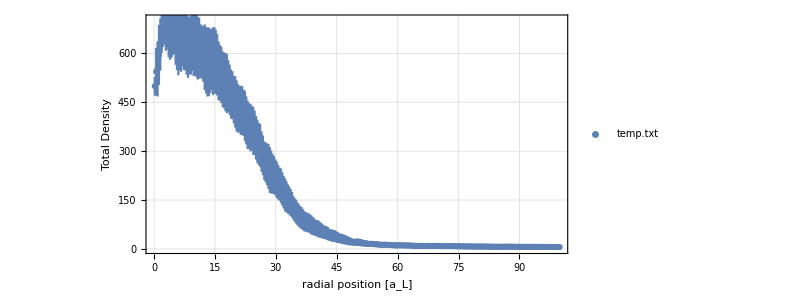

```mathematica
ErrorListPlot[datainput,GridLines->Automatic,ImageSize->600,Frame->True,FrameLabel->{"radial position [a_L]","Total Density"},LabelStyle->Directive[16,Bold,Black],AspectRatio->.5,PlotLegends->Placed[LineLegend[{fname},LabelStyle->18],{Right,Top}]]
```

### Fitting Via Lookup Table

The fit comes from using lookup tables outputted by the QUEST QMC analysis that is done ahead of time. The results of the QMC calculation for varying temperature is stored in a text file. 

The fit output is report as (Nx6) data matrix. It is organized as (temperature (β),?,?,?,?,?)

Import the data.

```mathematica
ffitname="2.5Er_206G/results.txt";
fitdata=ToExpression[Import[ffitname,"TSV"]];
```

Display a list of all temperatures that are included in the calculations (in units of β).

```mathematica
tempβlist=Union[fitdata⟦All,1⟧]
tempβnum=Length[tempβlist];
```

{1.01833,1.0627,1.11111,1.16414,1.22249,1.287,1.3587,1.43885,1.52905,1.63132,1.74825,1.88324,2.04082,2.22717,2.45098,2.7248,3.06748,3.50877,4.09836,4.92611,6.17284,8.26446}